# Formulación de y para datos experimentales y para función dieléctrica de tipo Drude

## Para una dada

## Definiciones

```mathematica
h=4.135667696*10^(-15); (*eV s*)
ℏ=6.582119569*10^(-16); (*eV s*)
c=3*^17 ;(*nm s^-1*)
```

### Datos experimentales

```mathematica
ψn[n_,ρ_]:= ρ*SphericalBesselJ[n,ρ]
```

```mathematica
ξn[n_,ρ_]:=ρ*SphericalHankelH1[n,ρ]
```

```mathematica
dψn[n_,ρ_]:=-n *SphericalBesselJ[n,ρ]+ ρ * SphericalBesselJ[n-1,ρ] 
dξn[n_,ρ_]:=-n * SphericalHankelH1[n,ρ] + ρ* SphericalHankelH1[n-1,ρ]
```

```mathematica
mieCoefAn[np_,nm_,a_,λ_,n_]:=Module[{m,x,an},
						m=np/nm;
						x=(2 Pi nm a)/λ;							
						an=((m ψn[n,m x] dψn[n,x])-(ψn[n,x] dψn[n,m x]))/((m ψn[n,m x] dξn[n,x])-(ξn[n,x] dψn[n,m x])); 
						an]
```

```mathematica
mieCoefBn[np_,nm_,a_,λ_,n_]:=Module[{m,x,bn},
						m=np/nm;
						x=(2 Pi nm a)/λ;							
						bn=((ψn[n,m x] dψn[n,x])-(m ψn[n,x] dψn[n,m x]))/((ψn[n,m x] dξn[n,x])-(m ξn[n,x] dψn[n,m x]));
						bn]
```

```mathematica
mieQsca[np_,nm_,a_,λ_,nmax_]:=Module[{an,bn,k,Csca,Qsca},
an=mieCoefAn[np,nm,a,λ,Table[n,{n,nmax}]];
bn=mieCoefBn[np,nm,a,λ,Table[n,{n,nmax}]];
Csca= (λ^2 )/(2*π* Norm[nm]^2)*(Sum[(2 n +1)(Norm[an[[n]] ]^2+Norm[bn[[n]]] ^2),{n,nmax}]);
Qsca=Csca/(Pi* a^2) ;
{an,bn,Csca,Qsca}]
```

```mathematica
mieQext[np_,nm_,a_,λ_,nmax_]:=Module[{an,bn,Cext,Qext},
an=mieCoefAn[np,nm,a,λ,Table[n,{n,nmax}]];
bn=mieCoefBn[np,nm,a,λ,Table[n,{n,nmax}]];
Cext =(λ^2 )/(2*π* Norm[nm]^2)* Sum[(2 n +1)Re[an[[n]] + bn[[n]] ],{n,nmax}];
Qext=Cext/(Pi* a^2) ;{an,bn,Cext,Qext}]
```

### Modelo de Drude

```mathematica
ϵ[λ_,λp_,γ_]:=1-((2 Pi c/λp)^2/((2 Pi c/λ)((2 Pi c/λ)+ I γ)))(*recibe λ en nm*)
```

```mathematica
ϵmieCoefAn[nm_,a_,λ_,n_,λp_,γ_]:=Module[{np,m,x,an},
						np=Sqrt[1-((2 Pi c/λp)^2/((2 Pi c/λ)((2 Pi c/λ)+ I γ)))];
						m=np/nm;
						x=(2 Pi nm a)/λ;							
						an=((m ψn[n,m x] dψn[n,x])-(ψn[n,x] dψn[n,m x]))/((m ψn[n,m x] dξn[n,x])-(ξn[n,x] dψn[n,m x])); 
						an]
```

```mathematica
ϵmieCoefBn[nm_,a_,λ_,n_,λp_,γ_]:=Module[{np,m,x,bn},
						np=Sqrt[1-((2 Pi c/λp)^2/((2 Pi c/λ)((2 Pi c/λ)+ I γ)))];
						m=np/nm;
						x=(2 Pi nm a)/λ;							
						bn=((ψn[n,m x] dψn[n,x])-(m ψn[n,x] dψn[n,m x]))/((ψn[n,m x] dξn[n,x])-(m ξn[n,x] dψn[n,m x]));
						bn]
```

```mathematica
ϵmieQsca[nm_,a_,λ_,nmax_,λp_,γ_]:=Module[{an,bn,k,Csca,Qsca},
an=ϵmieCoefAn[nm,a,λ,Table[n,{n,nmax}],λp,γ];
bn=ϵmieCoefBn[nm,a,λ,Table[n,{n,nmax}],λp,γ];
Csca= (λ^2 )/(2*π* Norm[nm]^2)*(Sum[(2 n +1)(Norm[an[[n]] ]^2+Norm[bn[[n]]] ^2),{n,nmax}]);
Qsca=Csca/(Pi* a^2) ;
{an,bn,Csca,Qsca}]
```

```mathematica
ϵmieQext[nm_,a_,λ_,nmax_,λp_,γ_]:=Module[{an,bn,Cext,Qext},
an=ϵmieCoefAn[nm,a,λ,Table[n,{n,nmax}],λp,γ];
bn=ϵmieCoefBn[nm,a,λ,Table[n,{n,nmax}],λp,γ];
Cext =(λ^2 )/(2*π* Norm[nm]^2)* Sum[(2 n +1)Re[an[[n]] + bn[[n]] ],{n,nmax}];
Qext=Cext/(Pi* a^2) ;
{an,bn,Cext,Qext}]
```

## Cálculos

### Criterio de Wiscombe

```mathematica
criterioWiscombe[nm_,a_,λ_]:=Module[{x,Wiscombe},
						x=(2 Pi nm a)/λ;							
						Wiscombe=Round[x+ 4*x^(1/3)+2];
						Wiscombe]
```

### Modelo de Drude

#### Para ℏω = 4.3 eV, ℏγ = 0.15 eV y a = 30 nm

```mathematica
criterioWiscombe[1.33,30,830]
```

5

```mathematica
qextDrude15=Table[{(h c)/λ,ϵmieQext[1.33,30,λ,5,2 Pi c/(4.3/ℏ),0.15/ℏ][[4]]},{λ,310,830}];
qscaDrude15=Table[{(h c)/λ,ϵmieQsca[1.33,30,λ,5,2 Pi c/(4.3/ℏ),0.15/ℏ][[4]]},{λ,310,830}];
```

```mathematica
upperTicks=Module[{labels,positions},labels={100,350,450,550,650,750};
positions=h c/#&/@labels;
Transpose[{positions,labels}]];
upperTicksMinor=Module[{labels,positions,size},labels={100,200,250,300,400,500,600,700,800};
positions=h c/#&/@labels;
labels=""&/@Range[Length[labels]];
size={-0.005,0}&/@Range[Length[labels]];
Transpose[{positions,labels,size}]];
```

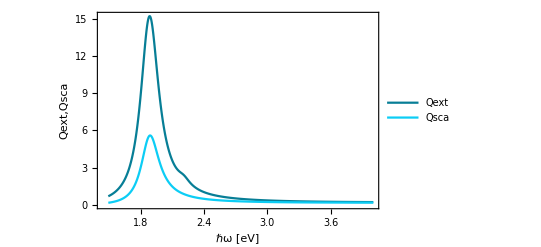

```mathematica
drude1=ListLinePlot[{Style[qextDrude15,RGBColor[0.027,0.494,0.588]],Style[qscaDrude15,RGBColor[0.047,0.804,0.961]]},Frame->True,FrameStyle->Directive[Black,FontFamily->"Times",10],FrameLabel->{{Style["Qext,Qsca",Black,12],None},{Style["ℏω [eV]",Black,12],Style["λ [nm]",Black,12]}},LabelStyle->Directive[Black, 15],FrameTicks->{{Automatic,None},{Automatic,Join[upperTicks,upperTicksMinor]}},PlotRange->All,PlotLegends->Placed[LineLegend[{Style[#,FontFamily->"Times",12]&/@{"Qext","Qsca"}},LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->LightGray]&)],{0.8,0.7}]]
```

```mathematica
Export["drude1.pdf",drude1]
```

drude1.pdf

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["drude1.svg"]]]
```

Variación de Qext y Qsca en función del radio

```mathematica
qextDrude10=Table[{(h c)/λ,ϵmieQext[1.33,#,λ,5,2 Pi c/(4.3/ℏ),0.15/ℏ][[4]]},{λ,310,830}]&/@{10,30,100};
qscaDrude12=Table[{(h c)/λ,ϵmieQsca[1.33,#,λ,5,2 Pi c/(4.3/ℏ),0.15/ℏ][[4]]},{λ,310,830}]&/@{10,30,100};
```

```mathematica
upperTicks=Module[{labels,positions},labels={100,350,450,550,650,750};
positions=h c/#&/@labels;
Transpose[{positions,labels}]];
upperTicksMinor=Module[{labels,positions,size},labels={100,200,250,300,400,500,600,700,800};
positions=h c/#&/@labels;
labels=""&/@Range[Length[labels]];
size={-0.005,0}&/@Range[Length[labels]];
Transpose[{positions,labels,size}]];
```

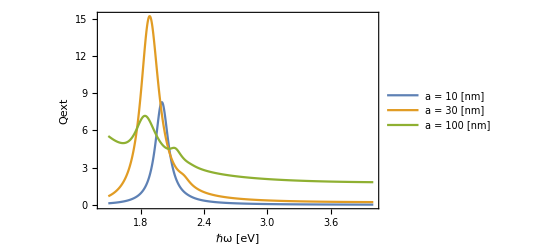

```mathematica
drude11=ListLinePlot[qextDrude10,Frame->True,FrameStyle->Directive[Black,FontFamily->"Times",10],FrameLabel->{{Style["Qext",Black,12],None},{Style["ℏω [eV]",Black,12],Style["λ [nm]",Black,12]}},LabelStyle->Directive[Black, 15],FrameTicks->{{Automatic,None},{Automatic,Join[upperTicks,upperTicksMinor]}},PlotRange->All,PlotLegends->Placed[LineLegend[{Style[#,FontFamily->"Times",12]&/@{"a = 10 [nm]","a = 30 [nm]","a = 100 [nm]"}},LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->LightGray]&)],{0.8,0.7}]]
```

```mathematica
Export["drude11.pdf",drude11]
```

drude11.pdf

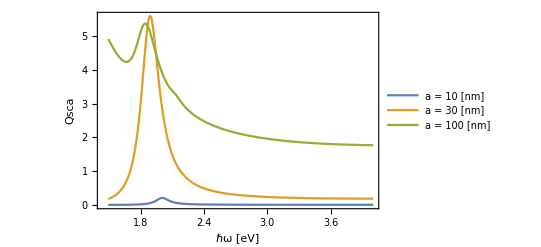

```mathematica
drude12=ListLinePlot[qscaDrude12,Frame->True,FrameStyle->Directive[Black,FontFamily->"Times",10],FrameLabel->{{Style["Qsca",Black,12],None},{Style["ℏω [eV]",Black,12],Style["λ [nm]",Black,12]}},LabelStyle->Directive[Black, 15],FrameTicks->{{Automatic,None},{Automatic,Join[upperTicks,upperTicksMinor]}},PlotRange->All,PlotLegends->Placed[LineLegend[{Style[#,FontFamily->"Times",12]&/@{"a = 10 [nm]","a = 30 [nm]","a = 100 [nm]"}},LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->LightGray]&)],{0.8,0.7}]]
```

```mathematica
Export["drude12.pdf",drude12]
```

drude12.pdf

#### Para ℏω = 10 eV, ℏγ = 0.15 eV y a = 30 nm

```mathematica
criterioWiscombe[1.33,30,800]
```

5

```mathematica
result20=Table[{(h c)/λ,ϵmieQext[1.33,30,λ,5,2 Pi c/(10/ℏ),0.15/ℏ][[4]]},{λ,120,800}];
result21=Table[{(h c)/λ,ϵmieQsca[1.33,30,λ,5,2 Pi c/(10/ℏ),0.15/ℏ][[4]]},{λ,120,800}];
```

```mathematica
upperTicks1=Module[{labels,positions},labels={1,150,200,250,300,450,600,800};
positions=h c/#&/@labels;
Transpose[{positions,labels}]];
upperTicksMinor1=Module[{labels,positions,size},labels={125,165,225,240,325,350,400,475,500,550,650,700,750,800};
positions=h c/#&/@labels;
labels=""&/@Range[Length[labels]];
size={-0.005,0}&/@Range[Length[labels]];
Transpose[{positions,labels,size}]];
```

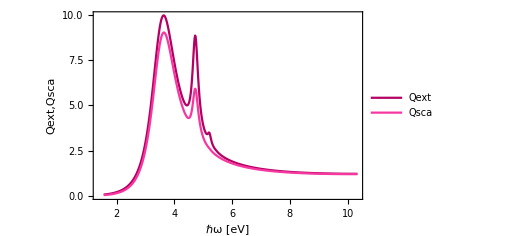

```mathematica
drude2=ListLinePlot[{Style[result20,RGBColor[0.702,0,0.384]],Style[result21,RGBColor[0.969,0.216,0.627]]},Frame->True,FrameStyle->Directive[Black,FontFamily->"Times",10],FrameLabel->{{Style["Qext,Qsca",Black,12],None},{Style["ℏω [eV]",Black,12],Style["λ [nm]",Black,12]}},LabelStyle->Directive[Black, 15],FrameTicks->{{Automatic,None},{Automatic,Join[upperTicks1,upperTicksMinor1]}},PlotRange->All,PlotLegends->Placed[LineLegend[{Style[#,FontFamily->"Times",12]&/@{"Qext","Qsca"}},LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->LightGray]&)],{0.8,0.7}]]
```

```mathematica
Export["drude2.pdf",drude2]
```

drude2.pdf

Variación de Qext y Qsca en función del radio

```mathematica
result201=Table[{(h c)/λ,ϵmieQext[1.33,#,λ,5,2 Pi c/(10/ℏ),0.15/ℏ][[4]]},{λ,120,800}]&/@{10,30,100};
result202=Table[{(h c)/λ,ϵmieQsca[1.33,#,λ,5,2 Pi c/(10/ℏ),0.15/ℏ][[4]]},{λ,120,800}]&/@{10,30,100};
```

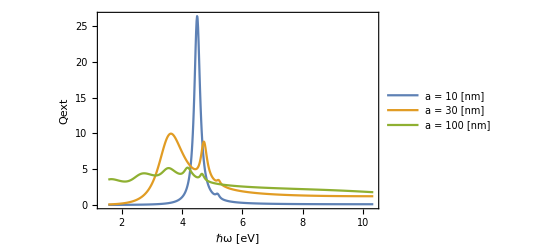

```mathematica
drude21=ListLinePlot[result201,Frame->True,FrameStyle->Directive[Black,FontFamily->"Times",10],FrameLabel->{{Style["Qext",Black,12],None},{Style["ℏω [eV]",Black,12],Style["λ [nm]",Black,12]}},LabelStyle->Directive[Black, 15],FrameTicks->{{Automatic,None},{Automatic,Join[upperTicks1,upperTicksMinor1]}},PlotRange->All,PlotLegends->Placed[LineLegend[{Style[#,FontFamily->"Times",12]&/@{"a = 10 [nm]","a = 30 [nm]","a = 100 [nm]"}},LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->LightGray]&)],{0.8,0.7}]]
```

```mathematica
Export["drude21.pdf",drude21]
```

drude21.pdf

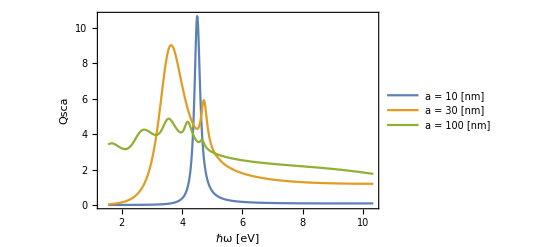

```mathematica
drude22=ListLinePlot[result202,Frame->True,FrameStyle->Directive[Black,FontFamily->"Times",10],FrameLabel->{{Style["Qsca",Black,12],None},{Style["ℏω [eV]",Black,12],Style["λ [nm]",Black,12]}},LabelStyle->Directive[Black, 15],FrameTicks->{{Automatic,None},{Automatic,Join[upperTicks1,upperTicksMinor1]}},PlotRange->All,PlotLegends->Placed[LineLegend[{Style[#,FontFamily->"Times",12]&/@{"a = 10 [nm]","a = 30 [nm]","a = 100 [nm]"}},LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->LightGray]&)],{0.8,0.7}]]
```

```mathematica
Export["drude22.pdf",drude22]
```

drude22.pdf

#### Para ℏω = 13.142 eV, ℏγ = 0.197 eV y a = 60 nm

```mathematica
criterioWiscombe[1.33,60,500]
```

7

```mathematica
result30=Table[{λ,ϵmieQext[1.33,60,λ,7,2 Pi c/(13.142/ℏ),0.197/ℏ][[4]]},{λ,0.5,500}];
result31=Table[{λ,ϵmieQsca[1.33,60,λ,7,2 Pi c/(13.142/ℏ),0.197/ℏ][[4]]},{λ,0.5,500}];
```

```mathematica
upperTicks2=Module[{labels,positions},labels={0.5,0.75,1,2,5,8,10,12,15,25,50};
positions=h c/#&/@labels;
Transpose[{positions,labels}]];
upperTicksMinor2=Module[{labels,positions,size},labels={0.2,0.6,0.9,1.25,3,4.5,6,7,7.7,9,11};
positions=h c/#&/@labels;
labels=""&/@Range[Length[labels]];
size={-0.005,0}&/@Range[Length[labels]];
Transpose[{positions,labels,size}]];
```

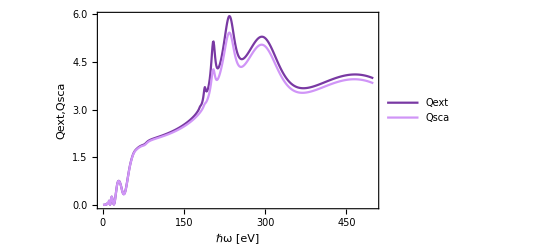

```mathematica
drude3=ListLinePlot[{Style[result30,RGBColor[0.475,0.224,0.639]],Style[result31,RGBColor[0.816,0.584,0.969]]},Frame->True,FrameStyle->Directive[Black,FontFamily->"Times",10],FrameLabel->{{Style["Qext,Qsca",Black,12],None},{Style["ℏω [eV]",Black,12],Style["λ [nm]",Black,12]}},LabelStyle->Directive[Black, 15],FrameTicks->{{Automatic,None},{Automatic,Join[upperTicks2,upperTicksMinor2]}},PlotRange->All,PlotLegends->Placed[LineLegend[{Style[#,FontFamily->"Times",12]&/@{"Qext","Qsca"}},LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->LightGray]&)],{0.8,0.3}]]
```

```mathematica
Export["drude3.pdf",drude3]
```

drude3.pdf

### Datos experimentales

#### Aluminio

Datos obtenidos de Rakic.b4  DOI: http://dx.doi.org/10.1063/1.370750

```mathematica
(*alum=Import["C:\\Users\\Poh\\Documents\\GitHub\\Servicio-Social\\Notebooks Mathematica\\Funciones dieléctricas\\Aluminio Rakic.csv"];*)
```

```mathematica
alum=Import["C:\\Users\\Lunita\\Documents\\GitHub\\Servicio-Social\\Notebooks Mathematica\\Funciones dieléctricas\\Aluminio Rakic.csv"];
```

```mathematica
alum1=Drop[Drop[alum,{208,415}],1];
λalum=alum1[[All,1]]*1000;
nalum=alum1[[All,2]];
alum2=Drop[alum,{1,209}];
kalum=alum2[[All,2]];
naluminio=nalum+ I kalum;
aluminio=Transpose[{λalum,naluminio}];
```

```mathematica
nindexalum=Interpolation[aluminio]
```

InterpolatingFunction[…]

```mathematica
criterioWiscombe[1.33,10,20]
```

13

```mathematica
varindep1=Table[{(h c)/λ,mieQext[nindexalum[λ],1,10,λ,13][[4]]},{λ,1,20}];
varindep2=Table[{(h c)/λ,mieQsca[nindexalum[λ],1,10,λ,13][[4]]},{λ,1,20}];
```

```mathematica
upperTicks3=Module[{labels,positions},labels={1,1.25,1.5,2,3.5,5,15};
positions=h c/#&/@labels;
Transpose[{positions,labels}]];
upperTicksMinor3=Module[{labels,positions,size},labels={1.15,1.35,1.75,2.75,4.5,7,9,12,15};
positions=h c/#&/@labels;
labels=""&/@Range[Length[labels]];
size={-0.005,0}&/@Range[Length[labels]];
Transpose[{positions,labels,size}]];
```

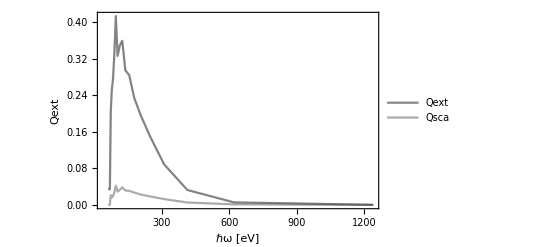

```mathematica
al1=ListLinePlot[{Style[varindep1,RGBColor[0.02,0.02,0.02,0.49]],Style[varindep2,RGBColor[0.188,0.188,0.173,0.4]]},Frame->True,FrameStyle->Directive[Black,FontFamily->"Times",10],FrameLabel->{{Style["Qext",Black,12],None},{Style["ℏω [eV]",Black,12],Style["λ [nm]",Black,12]}},LabelStyle->Directive[Black, 15],FrameTicks->{{Automatic,None},{Automatic,Join[upperTicks3,upperTicksMinor3]}},PlotRange->All,PlotLegends->Placed[LineLegend[{Style[#,FontFamily->"Times",12]&/@{"Qext","Qsca"}},LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->LightGray]&)],{0.8,0.7}]]
```

```mathematica
Export["alumninio.pdf",al1]
```

alumninio.pdf

#### Oro

Datos obtenidos de Johnson & Christy  DOI: https://doi.org/10.1103/PhysRevB.6.4370

```mathematica
(*au=Import["C:\\Users\\Poh\\Documents\\GitHub\\Servicio-Social\\Notebooks Mathematica\\Funciones dieléctricas\\Oro Johnson.csv"];*)
```

```mathematica
au=Import["C:\\Users\\Lunita\\Documents\\GitHub\\Servicio-Social\\Notebooks Mathematica\\Funciones dieléctricas\\Oro Johnson.csv"];
```

```mathematica
nau1=Drop[Drop[au,{51,101}],1];
kau1=Drop[au,{1,52}];
λAu=nau1[[All,1]]*1000; (*λ en nm*)
nau=nau1[[All,2]];
kAu=kau1[[All,2]];
nAu=nau+ I kAu;
aU=Transpose[{λAu,nAu}];
```

```mathematica
nindexau=Interpolation[aU];
```

```mathematica
criterioWiscombe[1,10,1937]
```

3

```mathematica
varindep20=Table[{(h c)/λ,mieQext[nindexau[λ],1,10,λ,3][[4]]},{λ,188,1937}];
varindep21=Table[{(h c)/λ,mieQsca[nindexau[λ],1,10,λ,3][[4]]},{λ,188,1937}];
```

```mathematica
upperTicks4=Module[{labels,positions},labels={200,350,500,650,800,1240};
positions=h c/#&/@labels;
Transpose[{positions,labels}]];
upperTicksMinor4=Module[{labels,positions,size},labels={250,300,350,400,450,550,600,700,650,900,1000};
positions=h c/#&/@labels;
labels=""&/@Range[Length[labels]];
size={-0.005,0}&/@Range[Length[labels]];
Transpose[{positions,labels,size}]];
```

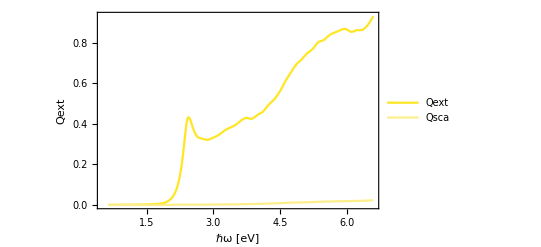

```mathematica
au1=ListLinePlot[{Style[varindep20,RGBColor[1,0.902,0.145]],Style[varindep21,RGBColor[0.988,0.937,0.545]]},Frame->True,FrameStyle->Directive[Black,FontFamily->"Times",10],FrameLabel->{{Style["Qext",Black,12],None},{Style["ℏω [eV]",Black,12],Style["λ [nm]",Black,12]}},LabelStyle->Directive[Black, 15],FrameTicks->{{Automatic,None},{Automatic,Join[upperTicks4,upperTicksMinor4]}},PlotRange->All,PlotLegends->Placed[LineLegend[{Style[#,FontFamily->"Times",12]&/@{"Qext","Qsca"}},LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->LightGray]&)],{0.8,0.7}]]
```

```mathematica
Export["oro.pdf",au1]
```

oro.pdf

### Plata

Datos obtenidos de Rakic.b4  DOI: http://dx.doi.org/10.1063/1.370750

```mathematica
(*ag=Import["C:\\Users\\Poh\\Documents\\GitHub\\Servicio-Social\\Notebooks Mathematica\\Funciones dieléctricas\\Plata Johnson.csv"];*)
```

```mathematica
ag=Import["C:\\Users\\Lunita\\Documents\\GitHub\\Servicio-Social\\Notebooks Mathematica\\Funciones dieléctricas\\Plata Johnson.csv"];
```

```mathematica
nag1=Drop[Drop[ag,{51,101}],1];
kag1=Drop[ag,{1,52}];
λAg=nag1[[All,1]]*1000;(*λ en nm*)
nAg=nag1[[All,2]];
kAg=kag1[[All,2]];
nAgg=nAg+ I kAg;
plata=Transpose[{λAg,nAgg}];
```

```mathematica
nindexplata=Interpolation[plata];
```

```mathematica
criterioWiscombe[1,10,1937]
```

3

```mathematica
varindepQextAg=Table[{(h c)/λ,mieQext[nindexplata[λ],1,10,λ,3][[4]]},{λ,188,1937}];
varindepQscaAg=Table[{(h c)/λ,mieQsca[nindexplata[λ],1,10,λ,3][[4]]},{λ,188,1937}];
```

```mathematica
upperTicksAg=Module[{labels,positions},labels={200,350,500,650,800,1240};
positions=h c/#&/@labels;
Transpose[{positions,labels}]];
upperTicksMinorAg=Module[{labels,positions,size},labels={250,300,350,400,450,550,600,700,650,900,1000};
positions=h c/#&/@labels;
labels=""&/@Range[Length[labels]];
size={-0.005,0}&/@Range[Length[labels]];
Transpose[{positions,labels,size}]];
```

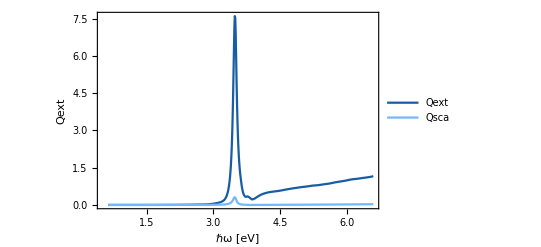

```mathematica
plata1=ListLinePlot[{Style[varindepQextAg,RGBColor[0.09,0.365,0.639]],Style[varindepQscaAg,RGBColor[0.447,0.722,1]]},Frame->True,FrameStyle->Directive[Black,FontFamily->"Times",10],FrameLabel->{{Style["Qext",Black,12],None},{Style["ℏω [eV]",Black,12],Style["λ [nm]",Black,12]}},LabelStyle->Directive[Black, 15],FrameTicks->{{Automatic,None},{Automatic,Join[upperTicksAg,upperTicksMinorAg]}},PlotRange->All,PlotLegends->Placed[LineLegend[{Style[#,FontFamily->"Times",12]&/@{"Qext","Qsca"}},LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->LightGray]&)],{0.8,0.7}]]
```

```mathematica
Export["plata.pdf",plata1]
```

plata.pdf

## Bismuto

Datos obtenidos de Hagemann  DOI: http://dx.doi.org/10.1063/1.370750

```mathematica
(*bism=Import["C:\\Users\\Poh\\Documents\\GitHub\\Servicio-Social\\Notebooks Mathematica\\Funciones dieléctricas\\Bismuto Hagemann.csv"];*)
```

```mathematica
bism=Import["C:\\Users\\Lunita\\Documents\\GitHub\\Servicio-Social\\Notebooks Mathematica\\Funciones dieléctricas\\Bismuto Hagemann.csv"];
```

```mathematica
nbism1=Drop[Drop[bism,{152,303}],1];
kbism1=Drop[bism,{1,153}];
λBism=nbism1[[All,1]]*1000;(*λ en nm*)
nBis=nbism1[[All,2]];
kBis=kbism1[[All,2]];
nBismuto=nBis+ I kBis;
bismuto=Transpose[{λBism,nBismuto}];
```

```mathematica
nindexbismuto=Interpolation[bismuto];
```

```mathematica
criterioWiscombe[1,10,619.9]
```

4

```mathematica
varindepBismuto1=Table[{(h c)/λ,mieQext[nindexbismuto[λ],1,10,λ,4][[4]]},{λ,2.48*10^(-3),619.9}];
varindepBismuto2=Table[{(h c)/λ,mieQsca[nindexbismuto[λ],1,10,λ,4][[4]]},{λ,2.48*10^(-3),619.9}];
```

```mathematica
upperTicksBi=Module[{labels,positions},labels={5,10,50,100,150,200,350,600};
positions=h c/#&/@labels;
Transpose[{positions,labels}]];
upperTicksMinorBi=Module[{labels,positions,size},labels={10,35,75,120,140,170,190,215,220,280,300,375,400,500};
positions=h c/#&/@labels;
labels=""&/@Range[Length[labels]];
size={-0.005,0}&/@Range[Length[labels]];
Transpose[{positions,labels,size}]];
```

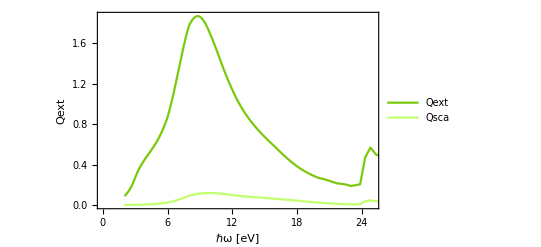

```mathematica
bismuto1=ListLinePlot[{Style[varindepBismuto1,RGBColor[0.482,0.788,0.051]],Style[varindepBismuto2,RGBColor[0.761,1,0.431]]},Frame->True,FrameStyle->Directive[Black,FontFamily->"Times",10],FrameLabel->{{Style["Qext",Black,12],None},{Style["ℏω [eV]",Black,12],Style["λ [nm]",Black,12]}},LabelStyle->Directive[Black, 15],FrameTicks->{{Automatic,None},{Automatic,Join[upperTicksBi,upperTicksMinorBi]}},PlotLegends->Placed[LineLegend[{Style[#,FontFamily->"Times",12]&/@{"Qext","Qsca"}},LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->LightGray]&)],{0.8,0.7}]]
```

```mathematica
Export["bismuto.pdf",bismuto1]
```

bismuto.pdf

## Óxido de magnesio

Datos obtenidos de Stephens and Malitson  DOI: http://dx.doi.org/10.1063/1.370750

```mathematica
(*mgO=Import["C:\\Users\\Poh\\Documents\\GitHub\\Servicio-Social\\Notebooks Mathematica\\Funciones dieléctricas\\Óxido de magnesio Stephens.csv"];*)
```

```mathematica
mgO=Import["C:\\Users\\Lunita\\Documents\\GitHub\\Servicio-Social\\Notebooks Mathematica\\Funciones dieléctricas\\Óxido de magnesio Stephens.csv"];
```

```mathematica
mgO1=Drop[mgO,1];
λMgO=mgO1[[All,1]]*1000 ;(*λ en nm*)
nMgO=mgO1[[All,2]];
nmgo=Transpose[{λMgO,nMgO}];
```

```mathematica
nindexMgO=Interpolation[nmgo];
```

```mathematica
criterioWiscombe[1,10,5400]
```

3

```mathematica
varindepQextMgO=Table[{(h c)/λ,mieQext[nindexMgO[λ],1,10,λ,3][[4]]},{λ,360,5400}];
varindepQscaMgO=Table[{(h c)/λ,mieQsca[nindexMgO[λ],1,10,λ,3][[4]]},{λ,360,5400}];
```

```mathematica
upperTicksBi=Module[{labels,positions},labels={360,500,1000,2500,5400};
positions=h c/#&/@labels;
Transpose[{positions,labels}]];
upperTicksMinorBi=Module[{labels,positions,size},labels={};
positions=h c/#&/@labels;
labels=""&/@Range[Length[labels]];
size={-0.005,0}&/@Range[Length[labels]];
Transpose[{positions,labels,size}]];
```

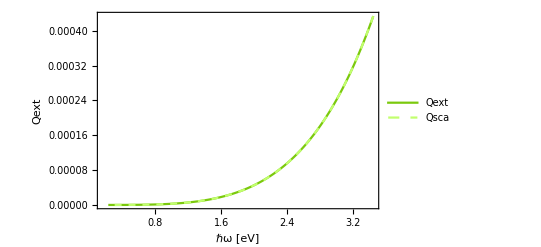

```mathematica
oximagn=ListLinePlot[{Style[varindepQextMgO,RGBColor[0.482,0.788,0.051]],Style[varindepQscaMgO,RGBColor[0.761,1,0.431],Dashed]},Frame->True,FrameStyle->Directive[Black,FontFamily->"Times",10],FrameLabel->{{Style["Qext",Black,12],None},{Style["ℏω [eV]",Black,12],Style["λ [nm]",Black,12]}},LabelStyle->Directive[Black, 15],FrameTicks->{{Automatic,None},{Automatic,Join[upperTicksBi,upperTicksMinorBi]}},PlotLegends->Placed[LineLegend[{Style[#,FontFamily->"Times",12]&/@{"Qext","Qsca"}},LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->LightGray]&)],{0.3,0.7}],PlotRange->All]
```

```mathematica
Export["oxidodemagnesio.pdf",oximagn]
```

oxidodemagnesio.pdf

## Para un n fija

## Definiciones

### Datos experimentales

```mathematica
nmieQsca[np_,nm_,a_,λ_,n_]:=Module[{an,bn,k,Csca,Qsca},
an=mieCoefAn[np,nm,a,λ,n];
bn=mieCoefBn[np,nm,a,λ,n];
Csca= (λ^2 )/(2*π* Norm[nm]^2)*((2 n +1)(Norm[an]^2+Norm[bn] ^2));
Qsca=Csca/(Pi* a^2) ;
{an,bn,Csca,Qsca}]
```

```mathematica
nmieQext[np_,nm_,a_,λ_,n_]:=Module[{an,bn,Cext,Qext},
an=mieCoefAn[np,nm,a,λ,n];
bn=mieCoefBn[np,nm,a,λ,n];
Cext =(λ^2 )/(2*π* Norm[nm]^2)* ((2 n +1)Re[an + bn]);
Qext=Cext/(Pi* a^2) ;{an,bn,Cext,Qext}]
```

### Modelo de Drude

```mathematica
nϵmieQsca[nm_,a_,λ_,n_,λp_,γ_]:=Module[{an,bn,k,Csca,Qsca,anCsca,anQsca},
an=ϵmieCoefAn[nm,a,λ,n,λp,γ];
bn=ϵmieCoefBn[nm,a,λ,n,λp,γ];
Csca= (λ^2 )/(2*π* Norm[nm]^2)*((2 n +1)(Norm[an]^2+Norm[bn] ^2));

anCsca= (λ^2 )/(2*π* Norm[nm]^2)*((2 n +1)(Norm[an]^2));
Qsca=Csca/(Pi* a^2) ;
anQsca=Csca/(Pi* a^2) ;
{an,bn,Csca,Qsca,anCsca,anQsca}]
```

```mathematica
nϵmieQext[nm_,a_,λ_,n_,λp_,γ_]:=Module[{an,bn,Cext,Qext,anCext,anQext},
an=ϵmieCoefAn[nm,a,λ,n,λp,γ];
bn=ϵmieCoefBn[nm,a,λ,n,λp,γ];
Cext =(λ^2 )/(2*π* Norm[nm]^2)*((2 n +1)Re[an+ bn]);
anCext =(λ^2 )/(2*π* Norm[nm]^2)*((2 n +1)Re[an+ bn]);
Qext=Cext/(Pi* a^2) ;
anQext=anCext/(Pi* a^2);
{an,bn,Cext,Qext,anCext,anQext}]
```

## Cálculos

### Modelo de Drude

#### Para ℏω = 4.3 eV, ℏγ = 0.15 eV y a = 30 nm

```mathematica
result123=Table[{(h c)/λ,nϵmieQext[1.33,30,λ,#,2 Pi c/(4.3/ℏ),0.15/ℏ][[4]]},{λ,310,830}]&/@{1,2,3};
```

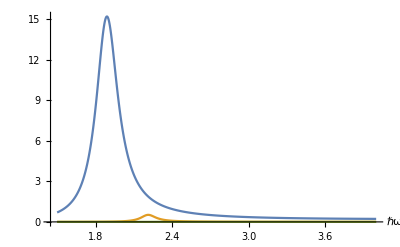

```mathematica
ListLinePlot[result123,AxesLabel->{"ℏω",""},PlotRange->All]
```

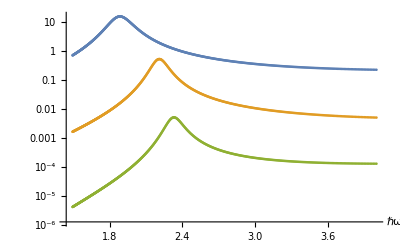

```mathematica
ListLogPlot[result123,AxesLabel->{"ℏω",""},PlotRange->All]
```

#### Para ℏω = 10 eV, ℏγ = 0.15 eV y a = 30 nm

```mathematica
result1=Table[{(h c)/λ,nϵmieQext[1.33,30,λ,#,2 Pi c/(10/ℏ),0.15/ℏ][[4]]},{λ,120,800}]&/@{1,2,3};
```

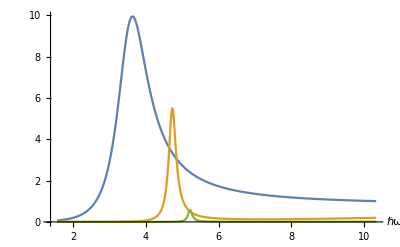

```mathematica
ListLinePlot[result1,AxesLabel->{"ℏω",""},PlotRange->All]
```

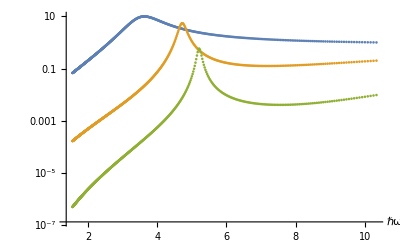

```mathematica
ListLogPlot[result1,AxesLabel->{"ℏω",""},PlotRange->All]
```

#### Para ℏω = 13.142 eV, ℏγ = 0.197 eV y a = 60 nm

```mathematica
result1=Table[{λ,nϵmieQext[1,60,λ,#,2 Pi c/(13.142/ℏ),0.197/ℏ][[6]]},{λ,0.5,500}]&/@{1,2,3,4};
```

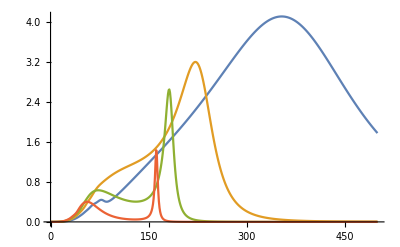

```mathematica
ListLinePlot[result1,AxesLabel->{"",""},PlotRange->All]
```